```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"];

survival={{{5,53/71},ErrorBar[{-53/71+71/72 (107/142-(13 √(23/71))/142),-53/71+71/72 (107/142+(13 √(23/71))/142)}]},{{10,35/69},ErrorBar[{-35/69+69/70 (71/138-(√(4829/69))/138),-35/69+69/70 (71/138+(√(4829/69))/138)}]},{{15,7/24},ErrorBar[{-7/24+72/73 (43/144-11/(144 √2)),-7/24+72/73 (43/144+11/(144 √2))}]},{{20,5/32},ErrorBar[{-5/32+64/65 (21/128-(√139)/256),-5/32+64/65 (21/128+(√139)/256)}]},{{25,12/73},ErrorBar[{-12/73+73/74 (25/146-(√(3001/73))/146),-12/73+73/74 (25/146+(√(3001/73))/146)}]},{{30,1/9},ErrorBar[{-1/9+72/73 (17/144-(√265)/432),-1/9+72/73 (17/144+(√265)/432)}]},{{50,4/65},ErrorBar[{-4/65+65/66 (9/130-(√(1041/65))/130),-4/65+65/66 (9/130+(√(1041/65))/130)}]}};


kB = 1.38 10^-23;
m=2.21 10^-25;
wr=.5;
T=50 10^-6;
(*tof in us, wr in um*)
data=Reap[
Do[
V=2 wr /tof;
p=0.8(1-Integrate[4π (m/(2π kB T))^(3/2)v^2 Exp[-(m v^2)/(2 kB T)],{v,V,Infinity}]);
Sow[{tof,p}]
,{tof,.1,50,2}]
][[2,1]];
```

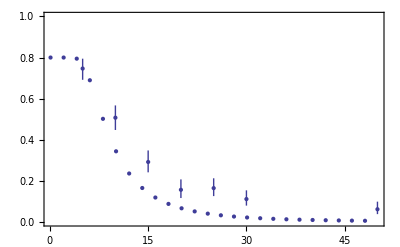

```mathematica
Show[{ErrorListPlot[survival,PlotRange->{All,{0,1}},Axes->False,Frame->True],
ListPlot[data,PlotRange->{All,{0,1}}]}]
```